# Name | M# |

## Models

Population models https://en.wikipedia.org/wiki/Population_model

Growth of population p'=(birth rate - death rate)p
Estimate death rate using life expectancy and birth rate using litter size etc.

Predator (wolf w) prey (moose m) https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations
m' | = |    α m | - | β m w
w' | = | -γ w | + | δ m w

Earth-Moon probe M=1/82.45, E=1-M, r_1=√((x+M)^2+y^2) and r_2=√((x-E)^2+y^2) 
	x'' | = |    2y' | + | x | - | (E(x+M))/r_1^3 | - | (M(x-E))/r_2^3
y'' | = | -2x' | + | y | - | (E y)/r_1^3 | - | (M y)/r_2^3

Mixing in Tanks y'=A y+f    with y(0)=y_0 volume v and salt s

v'(t) = rate in - rate out and s'(t) = rate in - rate out

```mathematica
A={{-7/100.0,5/200,0},{7/100,-9/200,2/700},{0,4/200,-4/700}};
f={6,0,0};y0={100,200,2100}; TMax=5000;
ySol=NDSolveValue[{y'[t]==A.y[t]+f,y[0]==y0},y,{t,0, TMax}];
TabView[{
"v_i vs t"->Plot[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"t","v_i"}],
"v_1 vs v_2 vs v_3"->ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"v_1","v_2","v_3"},PlotLabel->Eigenvalues[A]]}]
```

12

RLC circuits https://en.wikipedia.org/wiki/RLC_circuit
-Graphics-ODE
V+q' R + q'' L+q/C = 0                  
q is charge on the capacitor          
 I=i=q' is the current                          
Figure from wiki page above.        
R,L,and C are constants                 
As y'=A y+f system d/dt(q
i)=(0 | 1
-1/RC | -1/LR)(q
i)+(0
-V/L)

```mathematica
{v,r,l,c}={9,1.0,10,10}; TMax=100;
A ={{0,1},{-1/(r c), -1/(r l)}};f={0,-v/l};y0={0,0}; 
ySol=NDSolveValue[{y'[t]==A.y[t]+f,y[0]==y0},y,{t,0, TMax}];
TabView[{
"i & q vs t"->Plot[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"t","i & q"}],
"i vs q"->ParametricPlot[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"q","i"},PlotLabel->Eigenvalues[A]]}]
```

12

## Review y'=A y +b

Write down the complementary solution y_c=∑_(i=1)^n c_i y_i satisfying y_c'=A y_c

One solution when λ is real and A v=λ v
     e^(λ t)v

Two solutions when λ=a±b ⅈ and A (p + q ⅈ)=(a+b ⅈ)(p + q ⅈ)
       e^(a t)(cos(b t) p- sin(b t) q)  and e^(a t)(sin(b t) p+ cos(b t) q)

Two solutions when λ is repeated twice but there is only one eigenvector A v=λ v 
      e^(λ t)v  and t e^(λ t)v+e^(λ t)u 
 where u satisfies (A-λ I)u=v

Compute a particular solution y_p satisfying y_p'=A y_p+b

Guess the form (polynomial in t, exponentials e^(ω t), sin(ω t), …) for y_p if you can and compute the coefficients by substituting into the ODE.

Use variation of parameters y=Φ(t)u(t) where 
   u(t)=∫^t (Φ(τ))^-1 b(τ) dτ+c 
if you can not guess the form.

Write down the general solution y=y_c+y_p.

Substitute initial conditions (if there are) to determine the vector c=[c_1,c_2,…,c_n].

### Example

Solving higher order constant coefficient ODEs e.g.
	x''+2 x'+x=t

We can convert to a system by introducing v=x' like this
	x''=-2 x'-x+t
so rearranging gives
	x' | = |              v    
v' | = | -x -2v+t
which with y=(x
v) is 
	y'=(0 | 1
-1 | -2)y+(0
t)
The matrix has one eigen vector v=(-1
1) for a repeated eigenvector of λ=-1 so the complementary solution is 
	y_c=c_1 e^-t(-1
1)+c_2 e^-t(t(-1
1)+(-1
0))

```mathematica
MatrixForm[Eigensystem[A=({{0, 1}, {-1, -2}})]]
LinearSolve[A-(-1)IdentityMatrix[2],{-1,1}]
```

(-1 | -1
{-1,1} | {0,0})

{-1,0}

A particular solution is of the form
	y_p=u_0+t u_1
where the undetermined coefficients satisfy
	u_1=A(u_0+t u_1)+t(0
1)
Matching coefficients gives 
	0 | = | A u_1 | + | (0
1)
u_1 | = | A u_0 | + | (0
0)
rewriting gives
	((0 | 0
0 | 0) | -A
-A | (1 | 0
0 | 1))(u_0
u_1)=((0
1)
(0
0))

```mathematica
LinearSolve[ArrayFlatten[({{0, -A}, {-A, IdentityMatrix[2]}})],{0,1,0,0}]
```

{-2,1,1,0}

So u_0=(-2
1) and u_1=(1
0) and the general solution is 
	y=(x
v)=y_c+y_p=c_1 e^-t(-1
1)+c_2 e^-t(t(-1
1)+(-1
0))+(-2
1)+t(1
0)
We might only care about
	x(t)=-c_1 e^-t-c_2(1+t)e^-t-2+t 
People would describe this as two decaying transients and a linearly growing particular solution.

## Chapter 4:

Chapter 4 describes how to solve higher order constant coefficient linear ODEs directly without converting them to a system!  The Chapter 4 material matters because it is the way lots of scientists and engineers talk about simple equations such as
	m x''+c x'+k x=f_0 sin(ω t). 
This is the standard model for a mass-spring system with mass m, spring constant k, and linear damping coefficient c subject to a sinusoidal (angular frequency ω) force of f_0 Newtons.   In the real world, the damping c is usually small and the angular frequency of the force could be anywhere from slow ω<<1 to fast ω>>1.  We will see for the simple model there is a single angular frequency ω_0 near which a small force can produce an outsized response. Resonant responses can be disastrous.

### Chapter 4: y_c

To find the component solutions of 
	a_2 y''+a_1 y'+a_0 y=0
simply substitute y=e^(λ t) into the ODE to get
	a_2 λ^2 e^(λ t)+a_1 λ e^(λ t)+a_0 e^(λ t)=0
and cancel the exponential to get the characteristic polynomial
	a_2 λ^2+a_1 λ +a_0=0
Two distinct roots (λ_1 and λ_2) of this quadratic will give the complementary solution
	y_c=c_1 y_1+c_2 y_2 = c_1 e^(λ_1 t)+c_2 e^(λ_2 t)
Euler’s identity 
	e^((a ± ⅈ b)t)=e^(a t)(cos(b t) ± ⅈ sin(b t) )
splits complex root pairs λ=a±ⅈ b into two independent real solutions 
	y_1=e^(a t)cos(b t)
	y_2=e^(a t)sin(b t)

For a higher order ODE
	∑_(i=3)^n a_i y^(i)+a_2 y''+a_1 y'+a_0 y=0 
n roots λ_1,λ_2,…, λ_n of the characteristic polynomial would give n solutions
	y_i=e^(λ_(i t))
to build the complementary solution
	y_c=∑_(i=1)^n c_i y_i.

Multiplying by t  generates needed solutions for repeated roots. If λ is repeated twice 
	y_1=e^(λ t)  and y_2=t e^(λ t)
are solutions.  If λ is repeated three times then
	y_1=e^(λ t), y_2=t e^(λ t) and y_3=t^2 e^(λ t)
are solutions.

### Chapter 4: y_p undetermined coefficients

For 
	a_2 y''+a_1 y'+a_0 y=f
we can guess solution forms for simple right hand sides f.

If f is a polynomial guess a polynomial of the same order.

If f is an exponential guess the same type of exponential.

If f is a sine and/or cosine guess a sum of sines and cosines

Write down the form with appropriately named coefficients. Plug the form into the ODE to get equations to determine the coefficients.

The same process works for higher order ODEs.  A similar process works for any RHS that you get the same sort of terms when you differentiate.

### Chapter 4: General Solution and IC

The general solution of 
	∑_(i=0)^n a_i y^(i)=f	
is the sum of a particular solution and the complementary solution
	y=y_p+y_c=y_p+∑_(i=1)^n c_i y_i(t)
Plugging an appropriate set of initial conditions e.g. values for 
	y(0), y'(0), y''(0), …,y^(n-1)(0)
in gives n linear equations in the n unknowns c_1,c_2,…,c_n. Solving this linear system gives you the solution satisfying the initial conditions.

## Driven Mass-Spring system m y''+c y'+k y=f_0 sin(ω t)

The ODE
	m y''+c y'+k y=f_0 sin(ω t)
is the standard mass-spring model. The mass and spring are defined by the positive constants mass m, linear damping coefficient c, and spring constant k. The sinusoidal external force is described by the magnitude f_0 and the angular frequency ω.  The damping c is usually small and we are interested in the response of the system to a broad range of angular frequencies from slow ω<<1 to fast ω>>1.  We are going to see that there is a single angular frequency ω_0 near which small forces can produce outsized motions.

### Complementary Solution

The roots 
	λ_±=(-c ± √(c^2-4 k m))/(2m)	
of the characteristic polynomials
	m λ^2+ c λ+k=0 
give the complementary solution of 
	m y''+ c y'+k y=0.

If c=0 the roots are pure imaginary
	λ_±=(-0 ± √(0^2-4 k m))/(2m)=±ⅈ √(k/m).
writing
	ω_0=√(k/m)	
for the undamped (because c=0) natural frequency we see that both terms in the complementary solution
	c_1 cos(ω_0 t)+c_2 sin(ω_0 t)
oscillate at the natural frequency without decaying.

If c/(2m)<ω_0 the roots are complex
	λ_±=(-c ± √(c^2-4 k m))/(2m)=-c/(2m)±(√(c^2-4 k m))/(√((2 m)^2))=-c/(2m)±ⅈ √(k/m-(c/(2m))^2)
writing 
	ω_c=√(k/m-(c/(2m))^2)≤ω_0 
makes it easy to see that both terms
	 e^(-(c/(2m))t)(c_1 cos(ω_c t)+c_2 sin(ω_c t))
in the complementary solution decay exponentially like
	e^(-(c/(2m))t)
while oscillating slower than the undamped ω_0.

If c/(2m)>ω_0 the roots 
	λ_+=(-c + √(c^2-4 k m))/(2m)  and λ_-=(-c - √(c^2-4 k m))/(2m)
are real with λ_-<λ_+<0 and both terms in the complementary solution
	c_1 e^(λ_+t)+c_2 e^(λ_- t)
decay exponentially as t→∞  with the slower decay rate given by 
	λ_+=(-c + √(c^2-4 k m))/(2m)
so 
	c_1 e^(λ_+t)+c_2 e^(λ_- t)≈c_1 e^(λ_+t)as t→∞

These three cases are called:

Undamped (c=0) 
Oscillations with frequency ω_0=√(k/m) that do not decay.

Underdamped (c/(2m)<ω_0) 
Oscillations with frequency ω_c=√(k/m-(c/(2m))^2) that decay exponentially like e^(-(c/(2m))t)

Overdamped (c/(2m)>ω_0) 
No oscillations just exponential decay

### Particular Solution

The undetermined coefficient form for
	m y''+c y'+k y=f_0 sin(ω t)
is  
	y_p=a_1 cos(ω t)+a_2 sin(ω t)
with derivatives
	y'_p | = | -ω a_1 sin(ω t) | + | ω a_2 cos(ω t)
y''_p | = | -ω^2 a_1 cos(ω t) | - | ω^2 a_2 sin(ω t)
Substituting into the ODE gives 
	m(-ω^2 a_1 cos(ω t) | - | ω^2 a_2 sin(ω t))+
c(-ω a_1 sin(ω t) | + | ω a_2 cos(ω t))+
k(a_1 cos(ω t)+a_2 sin(ω t))=f_0 sin(ω t)

Matching the coefficients of sin(ω t) gives
	m(- | ω^2 a_2 sin(ω t))+
c(-ω a_1 sin(ω t))+
k(a_2 sin(ω t))=f_0 sin(ω t)
which implies
(Sin-Eq)	-m ω^2 a_2-c ω a_1+k a_2=f_0.

Matching the coefficients of cos(ω t) gives
	m(-ω^2 a_1 cos(ω t))+
c(ω a_2 cos(ω t))+
k(a_1 cos(ω t))=0
which implies
(Cos-Eq)	-m ω^2 a_1+c ω a_2+k a_1=0.

Combining the equations and organizing gives
(Sin-Eq)	(k-m ω^2)a_2-c ω a_1=f_0
(Cos-Eq)	(k-m ω^2)a_1+c ω a_2=0
Reordering the terms in the sine equation gives
	-c ω a_1 | + | (k-m ω^2)a_2 | = | f_0
(k-m ω^2)a_1 | + | c ω a_2 | = | 0	
which is simply
	(-c ω | k-m ω^2
k-m ω^2 | c ω)(a_1
a_2)=(f_0
0)
As always, call the matrix A then flashback to linear algebra.  Remember the solution to 
	A (a_1
a_2)=(f_0
0)
can be large if the determinant of A is small!  We can actually work out (by hand if we had to) how large the solution is 
	||(a_1
a_2)(||)^2=f_0^2/(k^2+c^2 ω^2-2 k m ω^2+m^2 ω^4)

```mathematica
Clear[m,k,c,ω]
A=({{-c ω, k-m ω^2}, {k-m ω^2, c ω}});
a=LinearSolve[A,{1,0}];
Simplify[a.a]
```

1/(k^2+c^2 ω^2-2 k m ω^2+m^2 ω^4)

we can tidy up the mess on the bottom quite a bit.  Divide top and bottom by m^2 to get
	1/(k^2+c^2 ω^2-2 k m ω^2+m^2 ω^4)=(1/m^2)/((k/m)^2+ (c/m)^2 ω^2-2 (k/m)  ω^2+ ω^4)
then recognize ω_0^2=k/m to get 
	1/((k/m)^2+ (c/m)^2 ω^2-2 (k/m)  ω^2+ ω^4)=1/((ω_0^2)^2+ (c/m)^2 ω^2-2 ω_0^2  ω^2+ ω^4)
then collect terms and complete the square to get
	1/(ω_0^4-2 ω_0^2  ω^2+ ω^4+ (c/m)^2 ω^2)=1/((ω^2-ω_0^2)^2+ (c/m)^2 ω^2)
Putting this all together we get
	||(a_1
a_2)(||)^2=(f_0^2/m^2)/((ω^2-ω_0^2)^2+ (c/m)^2 ω^2)

### General Solution and Interpretation y''+c/m y'+k/m y=f_0/m sin(ω t)

The general solution for the physically interesting underdamped case 0<c/(2m)<ω_0=√(k/m) is
	y=e^(-c/(2m)t)(c_1 cos(ω_c t)+ c_2 sin(ω_c t))+a_1 cos(ω t)+a_2 sin(ω t)	
where ||(a_1
a_2)(||)^2=(f_0^2/m^2)/((ω^2-ω_0^2)^2+ (c/m)^2 ω^2).  In other words, the response is an exponentially decaying transient with a steady state response that can be large if the damping is small and the driving frequency is near the natural frequency of the system.

```mathematica
m=1;
ω0=1;
Manipulate[
LogPlot[{√(1/((ω^2-ω0)^4+(c/m)^2 ω^2)),1/((c/m)ω0)},{ω,0, 2 ω0},PlotRange->All,

AxesLabel->{"ω","max |y|"},PlotLabel->"ω_0=1",PlotPoints->100,GridLines->Automatic],
{{c,0.001},0,0.1}]
```

### Simulation with c=0 m y''+0 y'+k y=f_0 sin(ω t)

When c=0 the complementary solution 
	y_c=c_1 cos(ω_0 t)+c_2 sin(ω_0 t)	
is undamped and the ICs are no longer “transient”!

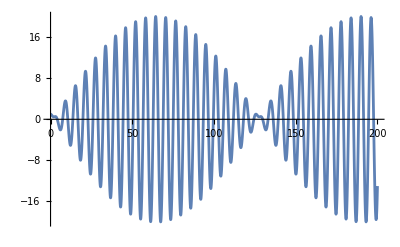

```mathematica
{m,c,k,f0,ω}={1.0,0,1.0,1.0,1.05};
TMax=200;
ySol=NDSolveValue[{
m y''[t]+c y'[t]+k y[t]==f0 Sin[ω t],
y[0]==1,
y'[0]==0},y,{t,0, TMax} ];
Plot[ySol[t],{t,0, TMax}]
```

Here is a short audio demonstration of this “beats” phenomena of two almost equal frequencies. 
https://www.youtube.com/watch?v=V8W4Djz6jnY

The “beats” come from the trig addition formulas
	  -Graphics-
https://en.wikipedia.org/wiki/List_of_trigonometric_identities#Sum-to-product_identities